```mathematica
productSumNumberQ[set_]:=Plus @@set==Times @@ set;
set[2]={2,2}; (* 4 *)
set[3]={1,2,3}; (* 6 *)
set[4]={1,1,2,4}; (* 8 *)
set[5]={1,1,2,2,2}; (* 8 *)
set[6]={1,1,1,1,2,6};(* 12 *)
set[7]={1,1,1,1,1,2,7};(* 14 *)
set[8]={1,1,1,1,1,2,2,3};(* 12 *)
set[9]={1,1,1,1,1,1,1,3,5};(* 15 *)
set[10]={1,1,1,1,1,1,1,1,4,4}; (* 16 *)
set[11]={1,1,1,1,1,1,1,1,1,2,11}; (* 22 *)
set[12]={1,1,1,1,1,1,1,1,2,2,2,2}; (* 16 *)
set[13]={1,1,1,1,1,1,1,1,1,1,1,3,7}; (* 21 *)
set[14]={1,1,1,1,1,1,1,1,1,1,1,1,2,14};(* 28 *)
set[100]={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,3,3,3}; (* 108 *)
set[101]={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,11,11}; (* 121 *)
Table[productSumNumberQ[set[n]],{n,2,14}]
{Plus @@ set[101],Times @@ set[101]==Plus @@ set[101]}
```

{True,True,True,True,True,True,True,True,True,True,True,True,True}

{121,True}

```mathematica
FactorInteger[42]
```

{{2,1},{3,1},{7,1}}

```mathematica
Subscript[N, 100]=Table[n-(n-1),{n,1,100}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Length[%]
```

100

```mathematica
FactorInteger[121]
set[101]={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,11,11};
{Times @@ set[101],Plus @@ set[101]}
```

{{11,2}}

{121,121}

```mathematica
Subsets[FactorInteger[42]]
```

{{},{{2,1}},{{3,1}},{{7,1}},{{2,1},{3,1}},{{2,1},{7,1}},{{3,1},{7,1}},{{2,1},{3,1},{7,1}}}

```mathematica
Max[Table[Plus@@Last/@ FactorInteger[n],{n,2,120000}]]
```

16

```mathematica
FactorInteger[120]
```

{{2,3},{3,1},{5,1}}

```mathematica
primeFactors[n_]:=ConstantArray @@@ FactorInteger[n]//Flatten;
```

```mathematica
primeFactors[60]
```

{2,2,3,5}

```mathematica
DeleteDuplicates[Subsets[primeFactors[120]]]
```

{{},{2},{3},{5},{2,2},{2,3},{2,5},{3,5},{2,2,2},{2,2,3},{2,2,5},{2,3,5},{2,2,2,3},{2,2,2,5},{2,2,3,5},{2,2,2,3,5}}

```mathematica
primeFactors[120]
```

{2,2,2,3,5}

```mathematica
Times @@@ DeleteDuplicates[Subsets[primeFactors[120]]]
```

{1,2,3,5,4,6,10,15,8,12,20,30,24,40,60,120}

```mathematica
primeFactors[n_]:=ConstantArray @@@ FactorInteger[n]//Flatten;
Times @@@ DeleteDuplicates[Subsets[primeFactors[120]]]
```

{1,2,3,5,4,6,10,15,8,12,20,30,24,40,60,120}

```mathematica
Table@@@ FactorInteger[120]//Flatten;
Times @@@ DeleteDuplicates[Subsets[%]]
```

{1,2,3,5,4,6,10,15,8,12,20,30,24,40,60,120}

```mathematica
Times @@@ {{}} == {1}
```

True

```mathematica
Drop[Apply[Times,DeleteDuplicates[Subsets[Flatten[Apply[Table,FactorInteger[120],2]]]],2],1]
```

{2,3,5,4,6,10,15,8,12,20,30,24,40,60,120}

```mathematica
Complement[Flatten[Table @@@ FactorInteger[120]],{2,3}]
```

{5}

```mathematica
Flatten[Table @@@ FactorInteger[120]]
```

{2,2,2,3,5}

```mathematica
PartitionsP[40]
```

37338

```mathematica
Length[Subsets[Table[x,{x,1,16}]]]
```

65536

```mathematica
16!
```

20922789888000

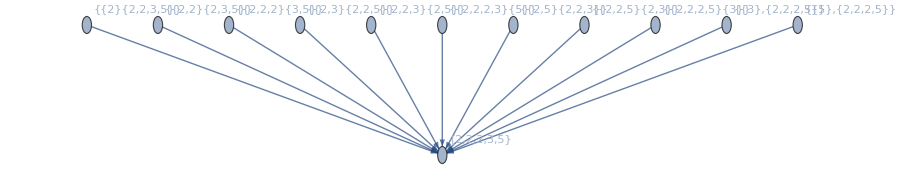

```mathematica
Graph[{
"{{2}{2,2,3,5}}"->"{2,2,2,3,5}",
"{{2,2}{2,3,5}}"->"{2,2,2,3,5}",
"{{2,2,2}{3,5}}"->"{2,2,2,3,5}",
"{{2,3}{2,2,5}}"->"{2,2,2,3,5}",
"{{2,2,3}{2,5}}"->"{2,2,2,3,5}",
"{{2,2,2,3}{5}}"->"{2,2,2,3,5}",
"{{2,5}{2,2,3}}"->"{2,2,2,3,5}",
"{{2,2,5}{2,3}}"->"{2,2,2,3,5}",
"{{2,2,2,5}{3}}"->"{2,2,2,3,5}",
"{{3},{2,2,2,5}}"->"{2,2,2,3,5}",
"{{5},{2,2,2,5}}"->"{2,2,2,3,5}"
},VertexLabels->"Name"]
```

```mathematica
"{{3},{2,2,2,5}}"->"{2,2,2,3,5}"
```

```mathematica
subsets=Drop[DeleteDuplicates[Subsets[Flatten[Table @@@ FactorInteger[120]]]],1]
```

{{2},{3},{5},{2,2},{2,3},{2,5},{3,5},{2,2,2},{2,2,3},{2,2,5},{2,3,5},{2,2,2,3},{2,2,2,5},{2,2,3,5},{2,2,2,3,5}}

```mathematica
Delete[{2,2,2,3,5},{2}]
```

{2,2,3,5}

```mathematica
a={2,2,2,3,5};
b={2,2,5};
Fold[DeleteCases[##,1,1]&,a,b]
```

{3}

```mathematica
Table[Fold[DeleteCases[##,1,1]&,Flatten[Table @@@ FactorInteger[120]],Drop[DeleteDuplicates[Subsets[Flatten[Table @@@ FactorInteger[120]]]],1][[i]]],{i,1,Length[Drop[DeleteDuplicates[Subsets[Flatten[Table @@@ FactorInteger[120]]]],1]]}]
```

{{2,2,3,5},{2,2,2,5},{2,2,2,3},{2,3,5},{2,2,5},{2,2,3},{2,2,2},{3,5},{2,5},{2,3},{2,2},{5},{3},{2},{}}

```mathematica
nOfK=Table[Infinity,{i,2,12000}];
ReplacePart[nOfK,2-> 42]
```

{∞,42,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,11763,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞,∞}
 |  |  |  |

```mathematica
Flatten[Table @@@ FactorInteger[120]]
```

{2,2,2,3,5}

```mathematica
primeFactors[n_]:=Flatten[Table @@@ FactorInteger[n]];
subsets[n_]:=Subsets[primeFactors[n]];
```

```mathematica
Max[Table[Length[Flatten[Table @@@ FactorInteger[n]]],{n,1,20000}]]
```

14

```mathematica
2^13
```

8192

```mathematica
Table[Prime[n],{n,1,1000000}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,999924,15485383,15485389,15485401,15485411,15485429,15485441,15485447,15485471,15485473,15485497,15485537,15485539,15485543,15485549,15485557,15485567,15485581,15485609,15485611,15485621,15485651,15485653,15485669,15485677,15485689,15485711,15485737,15485747,15485761,15485773,15485783,15485801,15485807,15485837,15485843,15485849,15485857,15485863}
 |  |  |  |